# Code

```mathematica
FromScript2DABG[v_,l_]:=
(* The input 
v is the set of nodes of the AB-graph
l is the list of speakers.
*)
Module[{i},
Graph[v,Table[l[[i-1]]->l[[i]],{i,2,Length[l]}],VertexLabels->Automatic,GraphLayout->"CircularEmbedding",VertexSize->Medium,VertexLabelStyle->Directive[Black,Italic,15],VertexLabels->Placed["Name",Center]]
(*the output is AB-directed graph *)
];
FromScript2ABG[v_,l_]:=
(* The input 
v is the set of nodes of the AB-graph
l is the list of speakers.
*)
Module[{i},
Graph[v,Table[l[[i-1]]<->   l[[i]],{i,2,Length[l]}],VertexLabels->Automatic,GraphLayout->"CircularEmbedding",VertexSize->Medium,VertexLabelStyle->Directive[Black,Italic,15],VertexLabels->Placed["Name",Center]]
(*the output is AB- graph *)
];
```

# Data

```mathematica
dir=NotebookDirectory[];
```

```mathematica
t1=Import[dir<>"romeo-and-juliet-z.xlsx"][[1]];
```

```mathematica
t1[[1]]
```

{Act-Scene,who's talking,What did he say,The number of words spoken,Word clock,Normalize word clock,Event clock,Normalize Event clock,M}

```mathematica
speakers=Drop[t1[[;;,2]],{1}]
```

{SAMPSON,GREGORY,SAMPSON,GREGORY,SAMPSON,GREGORY,SAMPSON,GREGORY,SAMPSON,GREGORY,SAMPSON,GREGORY,SAMPSON,GREGORY,SAMPSON,GREGORY,SAMPSON,GREGORY,SAMPSON,GREGORY,SAMPSON,GREGORY,SAMPSON,GREGORY,SAMPSON,ABRAHAM,SAMPSON,ABRAHAM,SAMPSON,GREGORY,SAMPSON,GREGORY,ABRAHAM,SAMPSON,ABRAHAM,SAMPSON,GREGORY,SAMPSON,ABRAHAM,SAMPSON,BENVOLIO,TYBALT,BENVOLIO,TYBALT,First Citizen,CAPULET,LADY CAPULET,CAPULET,MONTAGUE,LADY MONTAGUE,PRINCE,MONTAGUE,BENVOLIO,LADY MONTAGUE,BENVOLIO,MONTAGUE,BENVOLIO,MONTAGUE,BENVOLIO,MONTAGUE,BENVOLIO,MONTAGUE,BENVOLIO,ROMEO,BENVOLIO,ROMEO,BENVOLIO,ROMEO,BENVOLIO,ROMEO,BENVOLIO,ROMEO,BENVOLIO,ROMEO,BENVOLIO,ROMEO,BENVOLIO,ROMEO,BENVOLIO,ROMEO,BENVOLIO,ROMEO,BENVOLIO,ROMEO,BENVOLIO,ROMEO,BENVOLIO,ROMEO,BENVOLIO,ROMEO,BENVOLIO,ROMEO,BENVOLIO,ROMEO,BENVOLIO,CAPULET,PARIS,CAPULET,PARIS,CAPULET,Servant,BENVOLIO,ROMEO,BENVOLIO,ROMEO,BENVOLIO,ROMEO,Servant,ROMEO,Servant,ROMEO,Servant,ROMEO,Servant,ROMEO,Servant,ROMEO,Servant,ROMEO,Servant,BENVOLIO,ROMEO,BENVOLIO,ROMEO,LADY CAPULET,NURSE,JULIET,NURSE,JULIET,LADY CAPULET,NURSE,LADY CAPULET,NURSE,LADY CAPULET,NURSE,LADY CAPULET,NURSE,JULIET,NURSE,LADY CAPULET,JULIET,NURSE,LADY CAPULET,NURSE,LADY CAPULET,NURSE,LADY CAPULET,NURSE,LADY CAPULET,JULIET,Servant,LADY CAPULET,NURSE,ROMEO,BENVOLIO,ROMEO,MERCUTIO,ROMEO,MERCUTIO,ROMEO,MERCUTIO,ROMEO,MERCUTIO,BENVOLIO,ROMEO,MERCUTIO,ROMEO,MERCUTIO,ROMEO,MERCUTIO,ROMEO,MERCUTIO,ROMEO,MERCUTIO,ROMEO,MERCUTIO,ROMEO,MERCUTIO,BENVOLIO,ROMEO,BENVOLIO,First Servant,Second Servant,First Servant,Second Servant,First Servant,Second Servant,CAPULET,Second Capulet,CAPULET,Second Capulet,CAPULET,ROMEO,Servant,ROMEO,TYBALT,CAPULET,TYBALT,CAPULET,TYBALT,CAPULET,TYBALT,CAPULET,TYBALT,CAPULET,TYBALT,ROMEO,JULIET,ROMEO,JULIET,ROMEO,JULIET,ROMEO,JULIET,ROMEO,JULIET,NURSE,ROMEO,NURSE,ROMEO,BENVOLIO,ROMEO,CAPULET,JULIET,NURSE,JULIET,NURSE,JULIET,NURSE,JULIET,NURSE,JULIET,NURSE,JULIET,NURSE,Chorus,ROMEO,BENVOLIO,MERCUTIO,BENVOLIO,MERCUTIO,BENVOLIO,MERCUTIO,BENVOLIO,MERCUTIO,BENVOLIO,ROMEO,JULIET,ROMEO,JULIET,ROMEO,JULIET,ROMEO,JULIET,ROMEO,JULIET,ROMEO,JULIET,ROMEO,JULIET,ROMEO,JULIET,ROMEO,JULIET,ROMEO,JULIET,ROMEO,JULIET,ROMEO,JULIET,ROMEO,JULIET,ROMEO,JULIET,ROMEO,JULIET,ROMEO,JULIET,ROMEO,JULIET,NURSE,JULIET,NURSE,JULIET,ROMEO,JULIET,ROMEO,JULIET,ROMEO,JULIET,ROMEO,JULIET,ROMEO,JULIET,ROMEO,JULIET,ROMEO,JULIET,ROMEO,JULIET,ROMEO,FRIAR LAURENCE,ROMEO,FRIAR LAURENCE,ROMEO,FRIAR LAURENCE,ROMEO,FRIAR LAURENCE,ROMEO,FRIAR LAURENCE,ROMEO,FRIAR LAURENCE,ROMEO,FRIAR LAURENCE,ROMEO,FRIAR LAURENCE,ROMEO,FRIAR LAURENCE,ROMEO,FRIAR LAURENCE,MERCUTIO,BENVOLIO,MERCUTIO,BENVOLIO,MERCUTIO,BENVOLIO,MERCUTIO,BENVOLIO,MERCUTIO,BENVOLIO,MERCUTIO,BENVOLIO,MERCUTIO,BENVOLIO,MERCUTIO,ROMEO,MERCUTIO,ROMEO,MERCUTIO,ROMEO,MERCUTIO,ROMEO,MERCUTIO,ROMEO,MERCUTIO,ROMEO,MERCUTIO,ROMEO,MERCUTIO,ROMEO,MERCUTIO,ROMEO,MERCUTIO,ROMEO,MERCUTIO,ROMEO,MERCUTIO,ROMEO,MERCUTIO,BENVOLIO,MERCUTIO,BENVOLIO,MERCUTIO,ROMEO,MERCUTIO,BENVOLIO,NURSE,PETER,NURSE,MERCUTIO,NURSE,MERCUTIO,NURSE,MERCUTIO,NURSE,ROMEO,NURSE,ROMEO,NURSE,MERCUTIO,NURSE,BENVOLIO,MERCUTIO,ROMEO,MERCUTIO,ROMEO,MERCUTIO,NURSE,ROMEO,NURSE,PETER,NURSE,ROMEO,NURSE,ROMEO,NURSE,ROMEO,NURSE,ROMEO,NURSE,ROMEO,NURSE,ROMEO,NURSE,ROMEO,NURSE,ROMEO,NURSE,ROMEO,NURSE,PETER,NURSE,JULIET,NURSE,JULIET,NURSE,JULIET,NURSE,JULIET,NURSE,JULIET,NURSE,JULIET,NURSE,JULIET,NURSE,JULIET,NURSE,JULIET,NURSE,JULIET,FRIAR LAURENCE,ROMEO,FRIAR LAURENCE,JULIET,FRIAR LAURENCE,JULIET,ROMEO,JULIET,FRIAR LAURENCE,BENVOLIO,MERCUTIO,BENVOLIO,MERCUTIO,BENVOLIO,MERCUTIO,BENVOLIO,MERCUTIO,BENVOLIO,MERCUTIO,TYBALT,MERCUTIO,TYBALT,MERCUTIO,TYBALT,MERCUTIO,BENVOLIO,MERCUTIO,TYBALT,MERCUTIO,TYBALT,ROMEO,TYBALT,ROMEO,MERCUTIO,TYBALT,MERCUTIO,TYBALT,ROMEO,MERCUTIO,ROMEO,MERCUTIO,BENVOLIO,MERCUTIO,ROMEO,MERCUTIO,ROMEO,MERCUTIO,ROMEO,BENVOLIO,ROMEO,BENVOLIO,ROMEO,TYBALT,ROMEO,BENVOLIO,ROMEO,BENVOLIO,First Citizen,BENVOLIO,First Citizen,PRINCE,BENVOLIO,LADY CAPULET,PRINCE,BENVOLIO,LADY CAPULET,PRINCE,MONTAGUE,PRINCE,JULIET,NURSE,JULIET,NURSE,JULIET,NURSE,JULIET,NURSE,JULIET,NURSE,JULIET,NURSE,JULIET,NURSE,JULIET,NURSE,JULIET,NURSE,JULIET,NURSE,JULIET,NURSE,JULIET,FRIAR LAURENCE,ROMEO,FRIAR LAURENCE,ROMEO,FRIAR LAURENCE,ROMEO,FRIAR LAURENCE,ROMEO,FRIAR LAURENCE,ROMEO,FRIAR LAURENCE,ROMEO,FRIAR LAURENCE,ROMEO,FRIAR LAURENCE,ROMEO,FRIAR LAURENCE,ROMEO,FRIAR LAURENCE,ROMEO,FRIAR LAURENCE,NURSE,FRIAR LAURENCE,NURSE,FRIAR LAURENCE,NURSE,ROMEO,NURSE,ROMEO,NURSE,ROMEO,FRIAR LAURENCE,NURSE,ROMEO,NURSE,ROMEO,FRIAR LAURENCE,ROMEO,CAPULET,PARIS,LADY CAPULET,CAPULET,PARIS,CAPULET,PARIS,CAPULET,JULIET,ROMEO,JULIET,ROMEO,JULIET,ROMEO,NURSE,JULIET,NURSE,JULIET,ROMEO,JULIET,ROMEO,JULIET,ROMEO,JULIET,ROMEO,JULIET,LADY CAPULET,JULIET,LADY CAPULET,JULIET,LADY CAPULET,JULIET,LADY CAPULET,JULIET,LADY CAPULET,JULIET,LADY CAPULET,JULIET,LADY CAPULET,JULIET,LADY CAPULET,JULIET,LADY CAPULET,JULIET,LADY CAPULET,JULIET,LADY CAPULET,JULIET,LADY CAPULET,CAPULET,LADY CAPULET,CAPULET,JULIET,CAPULET,LADY CAPULET,JULIET,CAPULET,NURSE,CAPULET,NURSE,CAPULET,NURSE,CAPULET,LADY CAPULET,CAPULET,JULIET,LADY CAPULET,JULIET,NURSE,JULIET,NURSE,JULIET,NURSE,JULIET,NURSE,JULIET,FRIAR LAURENCE,PARIS,FRIAR LAURENCE,PARIS,FRIAR LAURENCE,PARIS,JULIET,PARIS,JULIET,FRIAR LAURENCE,PARIS,JULIET,PARIS,JULIET,PARIS,JULIET,PARIS,JULIET,PARIS,JULIET,PARIS,JULIET,FRIAR LAURENCE,PARIS,JULIET,FRIAR LAURENCE,JULIET,FRIAR LAURENCE,JULIET,FRIAR LAURENCE,JULIET,FRIAR LAURENCE,JULIET,CAPULET,Second Servant,CAPULET,Second Servant,CAPULET,NURSE,CAPULET,NURSE,CAPULET,JULIET,CAPULET,JULIET,CAPULET,JULIET,LADY CAPULET,CAPULET,LADY CAPULET,CAPULET,JULIET,LADY CAPULET,JULIET,LADY CAPULET,JULIET,LADY CAPULET,NURSE,CAPULET,NURSE,CAPULET,LADY CAPULET,CAPULET,First Servant,CAPULET,Second Servant,CAPULET,NURSE,LADY CAPULET,NURSE,LADY CAPULET,NURSE,LADY CAPULET,CAPULET,NURSE,LADY CAPULET,CAPULET,NURSE,LADY CAPULET,CAPULET,FRIAR LAURENCE,CAPULET,PARIS,LADY CAPULET,NURSE,PARIS,CAPULET,FRIAR LAURENCE,CAPULET,FRIAR LAURENCE,First Musician,NURSE,First Musician,PETER,First Musician,PETER,First Musician,PETER,First Musician,PETER,First Musician,PETER,First Musician,PETER,First Musician,Second Musician,PETER,Musician,PETER,Second Musician,PETER,Third Musician,PETER,First Musician,Second Musician,ROMEO,BALTHASAR,ROMEO,BALTHASAR,ROMEO,BALTHASAR,ROMEO,Apothecary,ROMEO,Apothecary,ROMEO,Apothecary,ROMEO,Apothecary,ROMEO,FRIAR JOHN,FRIAR LAURENCE,FRIAR JOHN,FRIAR LAURENCE,FRIAR JOHN,FRIAR LAURENCE,FRIAR JOHN,FRIAR LAURENCE,PARIS,PAGE,PARIS,ROMEO,BALTHASAR,ROMEO,BALTHASAR,ROMEO,PARIS,ROMEO,PARIS,ROMEO,PAGE,PARIS,ROMEO,FRIAR LAURENCE,BALTHASAR,FRIAR LAURENCE,BALTHASAR,FRIAR LAURENCE,BALTHASAR,FRIAR LAURENCE,BALTHASAR,FRIAR LAURENCE,BALTHASAR,FRIAR LAURENCE,BALTHASAR,FRIAR LAURENCE,JULIET,FRIAR LAURENCE,JULIET,First Watchman,JULIET,PAGE,First Watchman,Second Watchman,First Watchman,Third Watchman,First Watchman,PRINCE,CAPULET,LADY CAPULET,PRINCE,First Watchman,PRINCE,First Watchman,CAPULET,LADY CAPULET,PRINCE,MONTAGUE,PRINCE,MONTAGUE,PRINCE,FRIAR LAURENCE,PRINCE,FRIAR LAURENCE,PRINCE,BALTHASAR,PRINCE,PAGE,PRINCE,CAPULET,MONTAGUE,CAPULET,PRINCE}

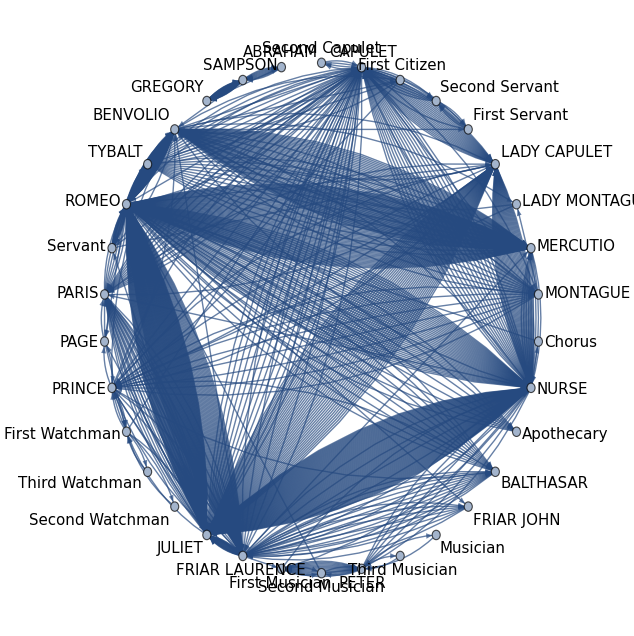

```mathematica
FromScript2DABG[Union[speakers],speakers]
```

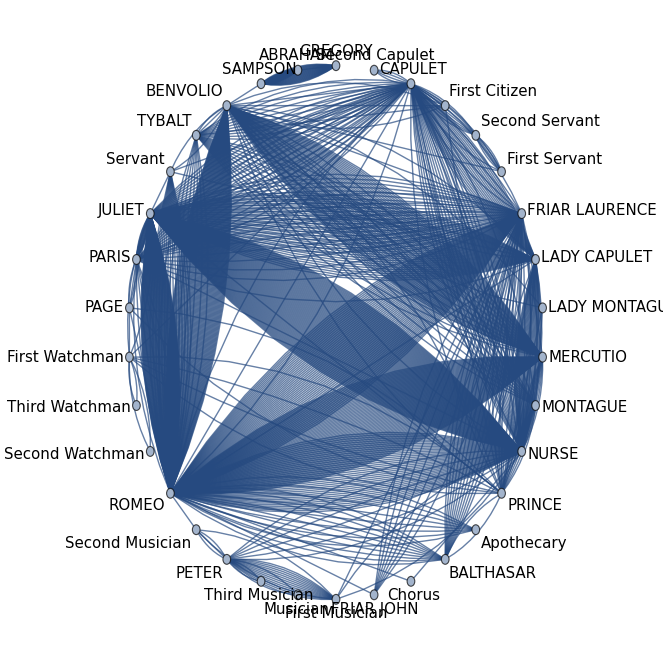

```mathematica
FromScript2ABG[Union[speakers],speakers]
```